# Riemann Solver

## HLLD

```mathematica
ClearAll["Global`*"]
τ=t/tp;
It[t_] = Ix*(27/4)^(1/4)*Sqrt[τ^2-τ^6];
rt[t_] = Ro*(1-τ^4);
dIdt[t_] = D[It[t], t];
drdt[t_] = D[rt[t], t];
b[t_] = (Sqrt[Subscript[μ, 0]]*It[t])/(2*π*rt[t]);
dedt[t_] =D[1/2 b[t]^2,t]//FullSimplify
dbdt[t_] = D[b[t],t]//FullSimplify
```

(Ix^2 t tp^2 (8.26993×10^-8 t^4+8.26993×10^-8 tp^4))/(Ro^2 (t^4-1. tp^4)^2)

(0.000143787 Ix (-(6 t^5)/tp^6+(2 t)/tp^2))/(Ro (1-t^4/tp^4) √(-t^6/tp^6+t^2/tp^2))+(0.0011503 Ix t^3 √(-t^6/tp^6+t^2/tp^2))/(Ro (1-t^4/tp^4)^2 tp^4)

NIntegrate::nlim: t = aa is not a valid limit of integration.

NIntegrate::nlim: t = bb is not a valid limit of integration.

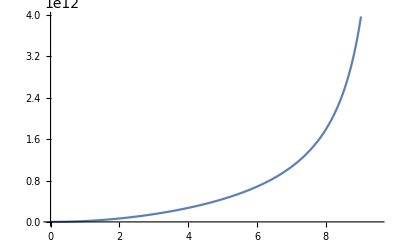

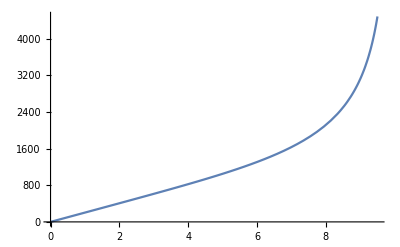

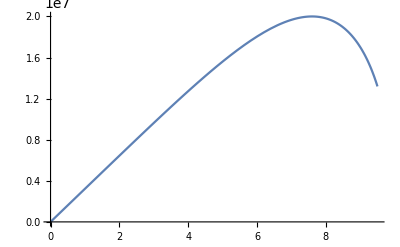

```mathematica
tp=100.0*^-9;
Ix = 20.0*^6;
Ro = 0.003168;
Subscript[μ, 0]=π*4.*^-7; (* permeability of free space *)
a=0.95*tp;
e[aa_]=NIntegrate[dedt[t], {t, 0.0, aa}];
bR[bb_] = NIntegrate[dbdt[t],{t, 0.0, bb}];
Plot[e[aa], {aa, 0.0, a}]
Plot[bR[bb]*Sqrt[Subscript[μ, 0]], {bb, 0.0, a}]
Plot[It[t], {t, 0, a}]
```

```mathematica
It[0.29585*tp]
tEndMatchPeterson=0.29585*tp
It[0.155*tp]
rt[0.155*tp]
It[0.04*tp]
It[0.172*tp]
```

9.50074×10^6

2.9585×10^-8

4.99531×10^6

0.00316617

1.28948×10^6

5.54235×10^6

```mathematica
jz[t_,η_] = (It[t]*Sqrt[Subscript[μ, 0]])/(2*π*rt[t]*Sqrt[η*tp])
```

(5.74111×10^9 √(1.×10^14 t^2-1.×10^42 t^6))/((1-1.×10^28 t^4) √η)

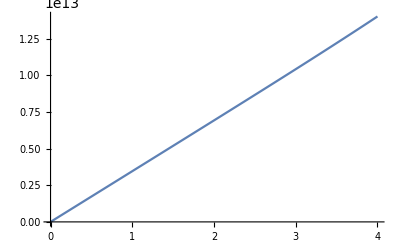

```mathematica
Plot[{jz[t,1*2.757*^-8]}, {t, 0, 0.4*tp}]
```

## Peterson 5a recover current density

```mathematica
ClearAll["Global`*"]
Subscript[ϵ, 0] = 8.8542*^-12; (* F m-1 Permittivity of free space *)
e = 1.6022*^-19; (* C elementary charge *)
Subscript[k, B] = 1.3807*^-23; (* J K-1 boltzmann constant *)
Subscript[μ, 0]=π*4.*^-7; (* permeability of free space *)
m = 4.482*^-26; (* kg mass of aluminum *)
Subscript[m, e]=9.1094*^-31; (* electron mass kg *)

(* From figure 5a *)
Rin = 336*^-6;
Rout = 343*^-6;
(* Create linear fit for pressure *)
b = 0;
a = (0.21*^6*(1*^5))/(Rout - Rin); (* 0.21 Mbar to Pa *)

pB[r_] =a*(r-Rin)+b; 
B = Sqrt[2*Subscript[μ, 0]*pB[r]]
J = 1/Subscript[μ, 0] Curl[{0,B, 0}, {r, θ, z}, "Cylindrical"]//FullSimplify;
J = J[[3]]
```

86832.2 √(-21/62500+r)

(-5.8043×10^9+2.59121×10^13 r)/(r √(-21+62500 r))

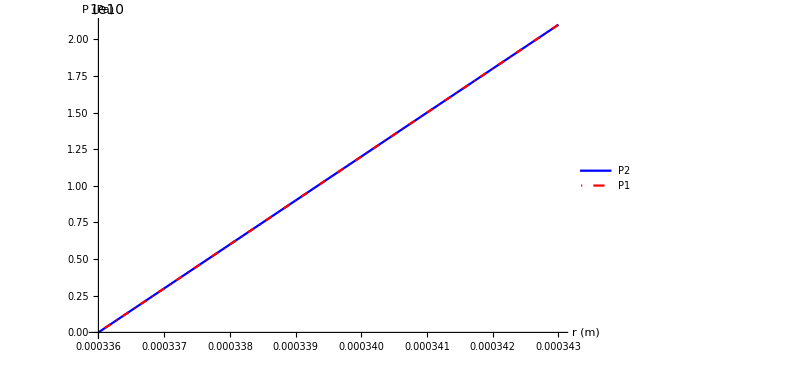

```mathematica
Ienc[R_] = Integrate[J*2*π*r,{r,336*^-6,R}]//FullSimplify;
B2 = 1/(2*π*r)*Subscript[μ, 0]*Ienc[r];
pB2[r_] = B2^2/(2*Subscript[μ, 0]);

Plot[{pB2[r],pB[r]}, {r, 336*^-6, 343*^-6},PlotStyle->{Blue,Directive[Red,DotDashed]}, PlotLegends->{"P2", "P1"},AxesLabel->{"r (m)","P (Pa)"},Ticks->{Automatic},ImageSize->600]
```